```mathematica
Needs["VectorFieldPlots`"];
SetDirectory[NotebookDirectory[]];
chi=ReadList["L_chi.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
mag=ReadList["L_mag.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
peak=ReadList["L_peak.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];
Dimensions[mag]
```

{450,1}

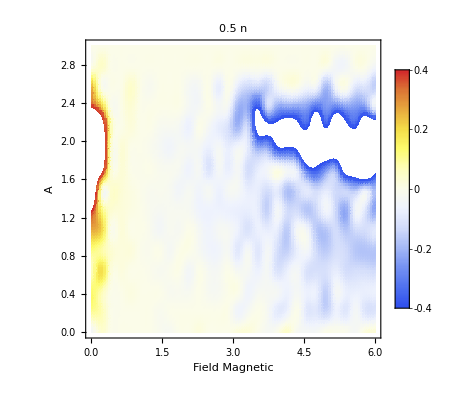

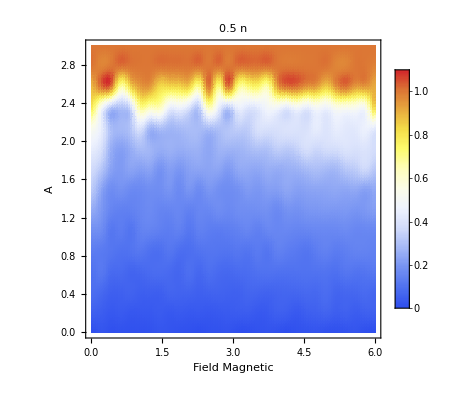

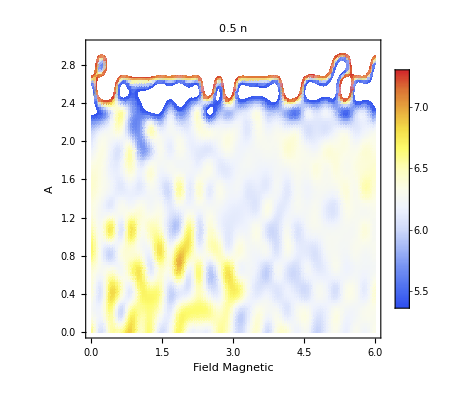

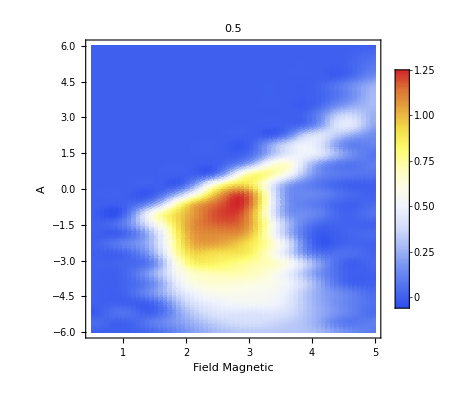

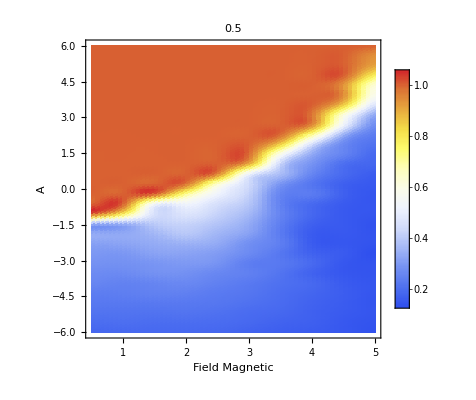

```mathematica
chi=ArrayReshape[chi,{15,30}];
ListDensityPlot[chi[[All,All]],DataRange->{{0,6},{0,3}},InterpolationOrder->2,ColorFunction->"TemperatureMap",PlotLabel-> n*0.5,PlotLegends->Automatic,AxesLabel->{Magnetic Field,A},PlotRange->{-0.4,0.4}]
mag=ArrayReshape[mag,{15,30}];
ListDensityPlot[mag[[All,All]],DataRange->{{0,6},{0,3}},InterpolationOrder->2,ColorFunction->"TemperatureMap",PlotLabel-> n*0.5,PlotLegends->Automatic,AxesLabel->{Magnetic Field,A}]
peak=ArrayReshape[peak,{15,30}];
ListDensityPlot[peak[[All,All]],DataRange->{{0,6},{0,3}},InterpolationOrder->2,ColorFunction->"TemperatureMap",PlotLabel-> n*0.5,PlotLegends->Automatic,AxesLabel->{Magnetic Field,A}]
```

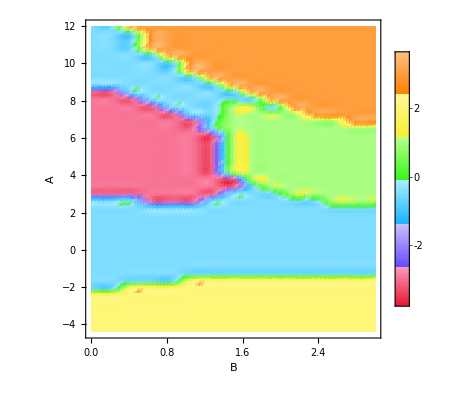

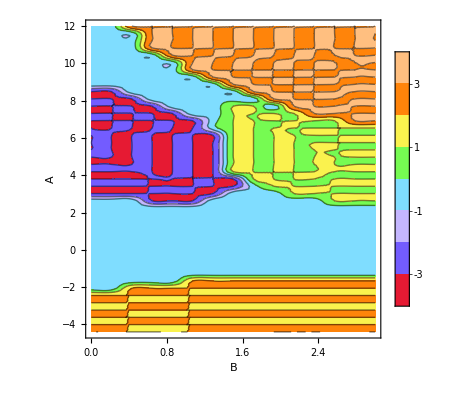

```mathematica
tot=ReadList["phase.csv",Number,RecordLists-> True,RecordSeparators->{"\n","\r\n","\r",","}];

tot=ArrayReshape[tot,{43,15,1}];
ListDensityPlot[tot[[All,All,n]],DataRange->{{0,3},{-4.4,12}},InterpolationOrder->2,ColorFunction->"BrightBands",PlotLegends->Automatic,AxesLabel->{B,A}]
ListContourPlot[tot[[All,All,n]],DataRange->{{0,3},{-4.4,12}},InterpolationOrder->2,ColorFunction->"BrightBands",PlotLegends->Automatic,AxesLabel->{B,A}]
```